## Description

Interception of rays by cylindrical receiver

## Functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Diameter and height

```mathematica
(* interception as a function of diameter and height *)
makeEtaDH[fileName_String]:=Module[
{data,dCoords,hCoords,etaMatrix,energyMax,funcEta},

(* import *)
data=Import[fileName];
dCoords=data[[1]]; (* diameters *)
hCoords=data[[2]]; (* heights *)
etaMatrix=data[[3;;-1,All]]; (* interception *)

(* padding *)
PrependTo[dCoords,0.];
PrependTo[hCoords,0.];
etaMatrix=Map[Prepend[#,0.]&,etaMatrix];
etaMatrix=Prepend[etaMatrix,Table[0.,{Dimensions[etaMatrix][[2]]}]];

(* normalization *)
energyMax=Max[Flatten@etaMatrix]; (* maximal intercepted energy *)
etaMatrix/=energyMax; 

(* interpolation *)
funcEta=ListInterpolation[
etaMatrix,{
{dCoords[[1]],dCoords[[-1]]},
{hCoords[[1]],hCoords[[-1]]}
},InterpolationOrder->3
]
]
```

```mathematica
(* optimal diameter, height, area, interception as a function of area *)
findOptimalForArea[funcEta_InterpolatingFunction,area_Real]:=Module[
{solution,x,d,h,eta},
solution=FindMaximum[
funcEta[x,area/(Pi*x)],
{x,1.*Sqrt[area/Pi],1.5*Sqrt[area/Pi]}
];
eta=solution[[1]];
d=x/.solution[[2]];
h=area/(Pi*d);
{d,h,area,eta}
]
```

### Area

```mathematica
(* interception as a function of area *)
makeEtaA[funcEtaDH_InterpolatingFunction]:=
Module[{dataAreaEta,funcEtaA},
dataAreaEta=Table[
findOptimalForArea[funcEtaDH,area][[3;;4]],
{area,5.,300.,5.}
];
PrependTo[dataAreaEta,{0.,0.}];
(*dataAreaEta[[All,2]]*=100.;*)

funcEtaA=Interpolation[dataAreaEta]
]
```

```mathematica
(* area as a function of interception *)
findAEta[funcEtaA_InterpolatingFunction,eta_Real]:=Module[
{r,rLims},
rLims=funcEtaA["Domain"][[1]];
r/.FindRoot[funcEtaA[r]==eta,{r,rLims[[1]],rLims[[2]]}]
]
```

### Costs

```mathematica
(* cost of receiver in M$ as a funcion of area according to SAM *)
funcCostA[area_Real]:=Module[{cRef=104.6,aRef=1571,k=0.7},
cRef*(area/aRef)^k
]
```

## Visual

### Diameter and height

```mathematica
isMajor[x_,x0_]:=Abs[(x/x0)-Round[x/x0]]<0.001
```

```mathematica
contourStyle[c_Real]:=Which[
isMajor[c,0.2],Directive[Black,AbsoluteThickness[2]],
isMajor[c,0.1],Directive[Black,AbsoluteThickness[1],Dashing[{0.02,0.01}]],
isMajor[c,0.01],Directive[Black,AbsoluteThickness[1],Dashing[{0.005,0.005}]]
];
```

```mathematica
contourLabel[c_Real]:=Module[{p},
p=Round[100*c];
Which[
isMajor[p,97],p,
isMajor[p,90],p,
isMajor[p,20],p,
isMajor[p,10],"",
isMajor[p,5],p
]
]
```

```mathematica
(* height as a function of diameter and interception, for contour labels *)
findHfromDEta[etaFunction_InterpolatingFunction,d_Real, eta_Real]:=Module[
{solution,h,hLims,x},
hLims=etaFunction["Domain"][[2]];
solution=FindRoot[
etaFunction[d,x]==eta,
{x,hLims[[1]],hLims[[2]]}
];
h=x/.solution
]
```

```mathematica
showEtaDH[funcEta_InterpolatingFunction]:=Module[
{contoursEta,
dLims,hLims,
figInterception,figArea,figOptimal,figInterceptionBar,figAreaBar,figPoints,
xA,xB,xC,yL},

{dLims,hLims}=funcEta["Domain"];
contoursEta=Join[Range[0.1,0.9,0.1],{0.95,0.96,0.97,0.98,0.99}];

figInterception=ContourPlot[
funcEta[d,h],
{d,dLims[[1]],dLims[[2]]},
{h,hLims[[1]],hLims[[2]]},
PlotRange->{{0,15},{0,15},{0,1}},
Contours->contoursEta,
ColorFunction->(ColorData["M10DefaultDensityGradient"][(#)]&),
ColorFunctionScaling->False,
ContourStyle->contourStyle/@contoursEta,
FrameLabel->{"Diameter d, m","Height h, m"},
FrameStyle->Directive[Black,FontFamily->"Arial",FontSize->14],
ImagePadding->{{1.,0.25},{0.75,0.25}}*72,
PlotRangePadding->0.,
ImageSize->{8,8}*72,
AspectRatio->Automatic,
MaxRecursion->3
];

figArea=ContourPlot[
Pi*d*h,
{d,0,15},
{h,0,15},
Contours->Range[0,300,25],
ContourStyle->Directive[White,Opacity[0.5],AbsoluteThickness[2.]],
ContourShading->None
];

figOptimal=ListPlot[
Table[
findOptimalForArea[funcEta,area][[1;;2]],
{area,25.,300.,25.}
],
Joined->True,
InterpolationOrder->1,
PlotStyle->Directive[RGBColor[0.25,0.5,0.5],AbsoluteThickness[3.],Opacity[0.5]]
];

xA=10.;
xB=11.5;
xC=(xA+xB)/2.;
yL=hLims[[1]]+0.9*(hLims[[2]]-hLims[[1]]);
yL=hLims[[1]]+0.9*(15.-hLims[[1]]);
figInterceptionBar=Graphics[{
Directive[White,Opacity[0.5]],
Rectangle[{xA,hLims[[1]]},{xB,hLims[[2]]}],
Directive[Black,Opacity[1.],FontFamily->"Arial",FontSize->14],
Text["Interception\nη, %",{xC,yL}],
Map[Text[contourLabel[#],{xC,findHfromDEta[funcEta,xC,#]}]&,contoursEta]
}];

xA=12.5;
xB=14.;
xC=(xA+xB)/2.;
figAreaBar=Graphics[{
Directive[White,Opacity[0.5]],
Rectangle[{xA,hLims[[1]]},{xB,hLims[[2]]}],
Directive[Black,Opacity[1.],FontFamily->"Arial",FontSize->14],
Text["Area\nA, m.b2",{xC,yL}],
Map[Text[#,{xC,#/(Pi*xC)}]&,Range[50,300,50]]
}];

figPoints=Graphics[{
PointSize[0.0175],
FontFamily->"Arial",FontSize->14,
Point[pASTRI],
Text["ASTRI",pASTRI,{-1.5,1.5}],
Point[pBest],
Text["Best",pBest,{1.5,-1.5}]
}];
Show[{figInterception,figArea,figOptimal,figInterceptionBar,figAreaBar,figPoints}]
]
```

### Area

```mathematica
plotStyle={
PlotStyle->Directive[RGBColor["#225F8E"],Thickness[0.005]],
PlotRangePadding->0,

GridLinesStyle->Directive[GrayLevel[0.7],Dashing[0.008]],

Axes->None,
Frame->True,
Filling->Axis,
FrameStyle->Directive[Black,FontFamily->"Arial",FontSize->14],

ImagePadding->{{1.,0.25},{0.75,0.25}}*72,
AspectRatio->0.45
};
```

## Parameters

```mathematica
pASTRI={diameterASTRI=15./2,heightASTRI=18.67/2}
areaASTRI=Pi*diameterASTRI*heightASTRI
costRecASTRI=funcCostA[areaASTRI]
```

{7.5,9.335}

219.951

26.4141

```mathematica
pBest={diameterBest=6.9762797883328,heightBest=9.705928735337176}
areaBest=Pi*diameterBest*heightBest
costRecBest=funcCostA[areaBest]
```

{6.97628,9.70593}

212.721

25.8033

## Calculations

### Diameter and height

```mathematica
funcEtaDH=makeEtaDH["C:\\Neo\\Programming\\CylindricalReceiver.csv"];
```

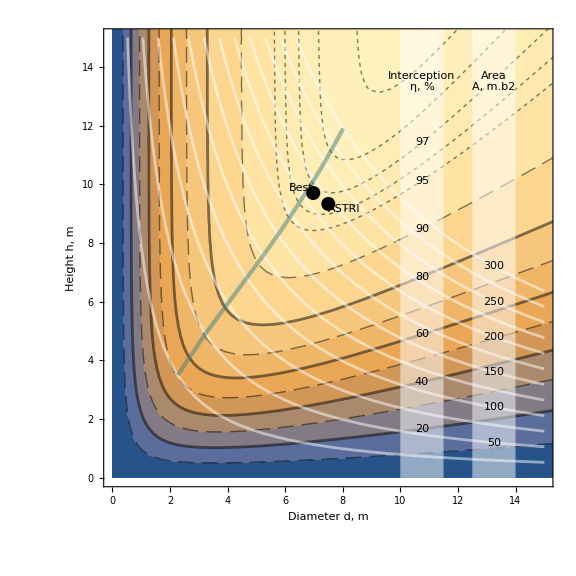

```mathematica
figEtaDH=showEtaDH[funcEtaDH]
```

```mathematica
(*Export["figEtaDH.png",figEtaDH];*)
```

```mathematica
funcEtaDH52=makeEtaDH["C:\\Neo\\Programming\\CylindricalReceiver52.csv"];
```

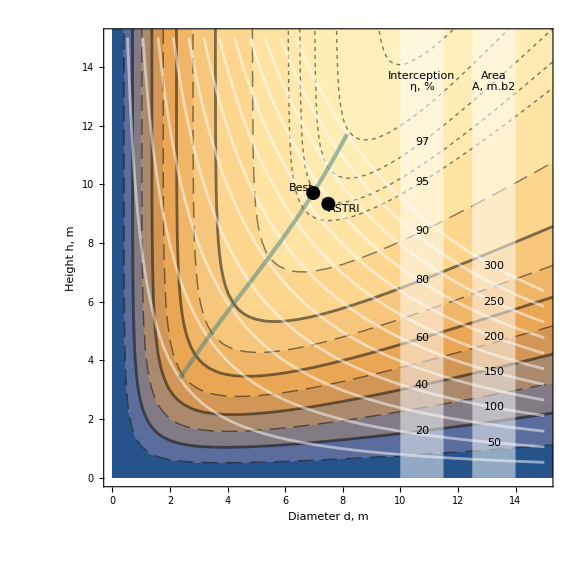

```mathematica
figEtaDH52=showEtaDH[funcEtaDH52]
```

```mathematica
(*Export["figEtaDH52.png",figEtaDH52];*)
```

### Area

```mathematica
funcEtaA=makeEtaA[funcEtaDH];
funcEtaA52=makeEtaA[funcEtaDH52];
```

```mathematica
(* gridlines for interception *)
levels={90.,95.};
```

```mathematica
legend=SwatchLegend[
{RGBColor["#225F8E"],RGBColor["#228E5F"]},
{"Fixed","Year"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->14],
LegendMarkers->{Graphics[{EdgeForm[],Rectangle[]}]}];
```

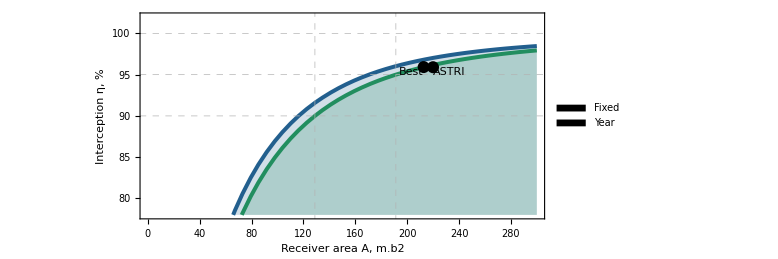

```mathematica
figEtaA=Plot[
{100.*funcEtaA[area],100.*funcEtaA52[area]},{area,0,300},
PlotRange->{Full,{78,102}},
PlotLegends->Placed[legend,{0.1,0.81}],
GridLines->{
Join[
Map[findAEta[funcEtaA52,#/100.]&,levels]
],
Join[levels,{100.}]
},
ImageSize->{8,4}*72,
FrameLabel->{"Receiver area A, m.b2","Interception η, %"},
PlotStyle->{
Directive[RGBColor["#225F8E"],Thickness[0.005]],
Directive[RGBColor["#228E5F"],Thickness[0.005]]
},
Evaluate[plotStyle],
Epilog->Module[{pA,pB},
pA={areaASTRI,100.*funcEtaDH52[diameterASTRI,heightASTRI]};
pB={areaBest,100.*funcEtaA52[areaBest]};
{
PointSize[0.015],
FontFamily->"Arial",FontSize->14,
Point[pA],
Text["ASTRI",pA,{-1,1.7}],
Point[pB],
Text["Best",pB,{1.,1.7}]
}]
]
```

```mathematica
(*Export["figEtaA.png",figEtaA];*)
```

## Costs

```mathematica
funcCKWH[area_]:=(193.6+funcCostA[area])/funcEtaA52[area];
areaBest=a/.FindMinimum[funcCKWH[a],{a,100,200}][[2]];
minCKWH=funcCKWH[areaBest];
funcCKWH[area_]:=(193.6+funcCostA[area])/funcEtaA52[area]/minCKWH;
```

```mathematica
{diameterBest,heightBest,areaBest,etaBest}=findOptimalForArea[funcEtaDH52,areaBest](* diameter, height, area, interception *)
costRecBest=funcCostA[areaBest]
```

{6.97628,9.70593,212.721,0.959191}

25.8033

```mathematica
savings=costRecASTRI-costRecBest
```

0.61078

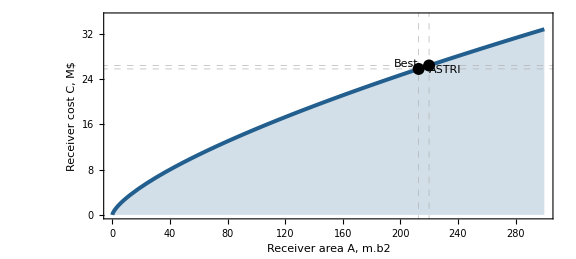

```mathematica
figCostA=Plot[
funcCostA[area],{area,0,300},
PlotRange->{All,{0,35}},
GridLines->{{areaBest,areaASTRI},{costRecBest,costRecASTRI}},
ImageSize->{8,4}*72,
FrameLabel->{"Receiver area A, m.b2","Receiver cost C, M$"},
 Evaluate[plotStyle],
Epilog->Module[{pA,pB},
pA={areaASTRI,funcCostA[areaASTRI]};
pB={areaBest,funcCostA[areaBest]};
{
PointSize[0.015],
FontFamily->"Arial",FontSize->14,
Point[pA],
Text["ASTRI",pA,{-1.5,1.7}],
Point[pB],
Text["Best",pB,{1.5,-1.7}]
}]
]
```

```mathematica
(*Export["figCostA.png",figCostA];*)
```

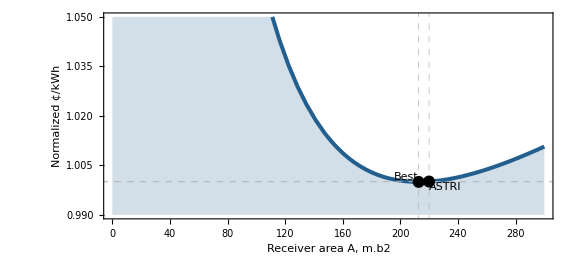

```mathematica
figCKWH=Plot[
funcCKWH[area],{area,0,300},
PlotRange->{Full,{0.99,1.05}},
GridLines->{{areaBest,220.},{1.,funcCKWH[areaASTRI]}},
ImageSize->{8,4}*72,
FrameLabel->{"Receiver area A, m.b2","Normalized  ¢/kWh"},
 Evaluate[plotStyle],
Epilog->Module[{pA,pB},
pA={areaASTRI,funcCKWH[areaASTRI]};
pB={areaBest,funcCKWH[areaBest]};
{
PointSize[0.015],
FontFamily->"Arial",FontSize->14,
Point[pA],
Text["ASTRI",pA,{-1.5,1.7}],
Point[pB],
Text["Best",pB,{1.5,-1.7}]
}]
]
```

```mathematica
(*Export["figCKWH.png",figCKWH];*)
```